```mathematica
Clear[toler,wava,prova];
Manipulate[toler*"行化简计算精度"+wava*"波函数量级"+prova*"概率值量级",{{toler,-5,"行化简计算精度"},-20,0,0.1},{{wava,4,"波函数量级"},-20,10,1},{{prova,8,"概率值量级"},-20,10,1},LocalizeVariables->False]
```

数值解：

【基态】能量
1.88338 meV 或 3.0134×10^-22 J

数值解：

【第1激发态】能量 
1.86605 meV 或 2.9857×10^-22 J

数值解：

【第2激发态】能量 
1.84679 meV 或 2.9549×10^-22 J

数值解：

【第3激发态】能量 
1.82519 meV 或 2.9203×10^-22 J

数值解：

【第4激发态】能量 
1.80071 meV 或 2.8811×10^-22 J

数值解：

【第5激发态】能量 
1.77263 meV 或 2.8362×10^-22 J

数值解：

【第6激发态】能量 
1.73995 meV 或 2.7839×10^-22 J

数值解：

【第7激发态】能量 
1.70119 meV 或 2.7219×10^-22 J

数值解：

【第8激发态】能量 
1.65413 meV 或 2.6466×10^-22 J

数值解：

【第9激发态】能量 
1.59513 meV 或 2.5522×10^-22 J

数值解：

【第10激发态】能量 
1.51781 meV 或 2.4285×10^-22 J

数值解：

【第11激发态】能量 
1.40942 meV 或 2.2551×10^-22 J

共12个态

【起始势阱形状】
左边阱宽：4.(纳米)，阱距 ：2.(纳米)，右边阱宽：4.(纳米)，
左势垒14.(meV)，2.24×10^-21(J)，
左势阱0(meV)，0
中间势垒0.(meV)，0.(J)，
右势阱0.(meV)，0.(J)，
右势垒7.(meV)，1.12×10^-21(J)

【结束势阱形状】
左边阱宽：4.(纳米)，阱距 ：2.(纳米)，右边阱宽：4.(纳米)，
左势垒3.(meV)，4.8×10^-22(J)，
左势阱0(meV)，0
中间势垒0.(meV)，0.(J)，
右势阱0.(meV)，0.(J)，
右势垒7.(meV)，1.12×10^-21(J)

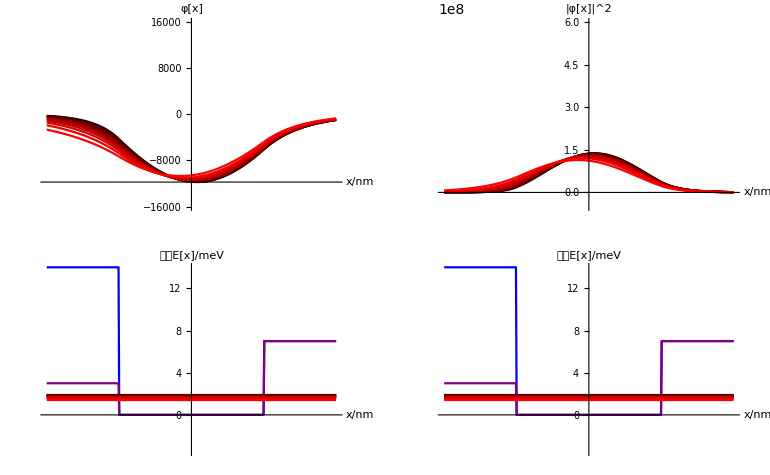

历史演化图像：没有启用。呈现初状态与末状态的对比

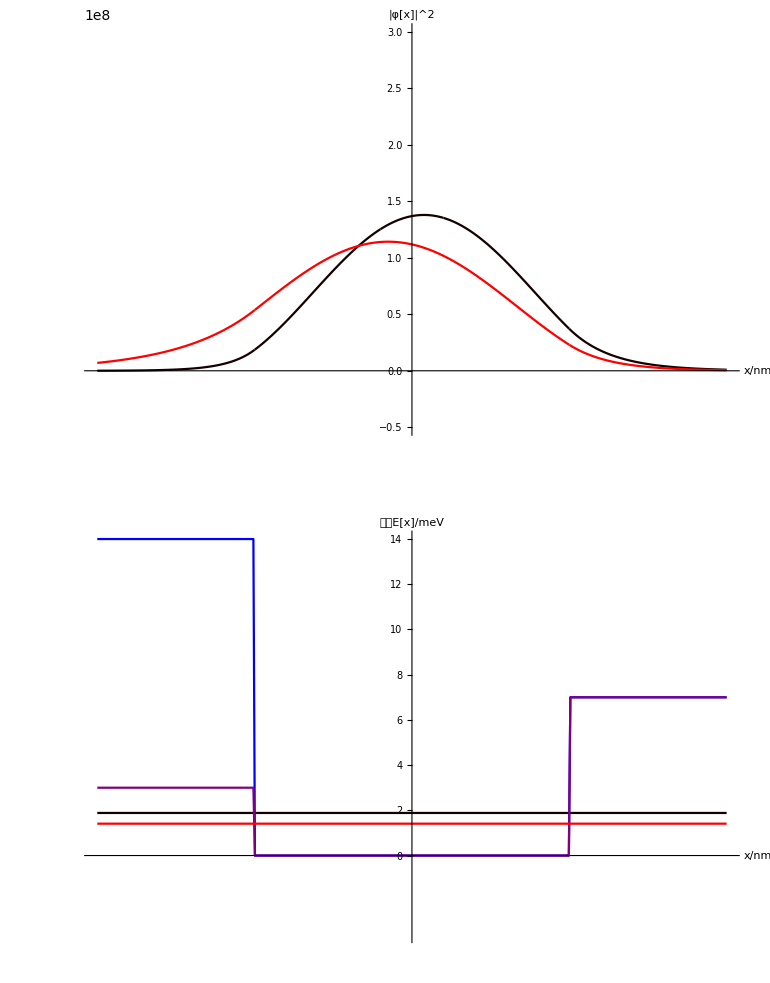

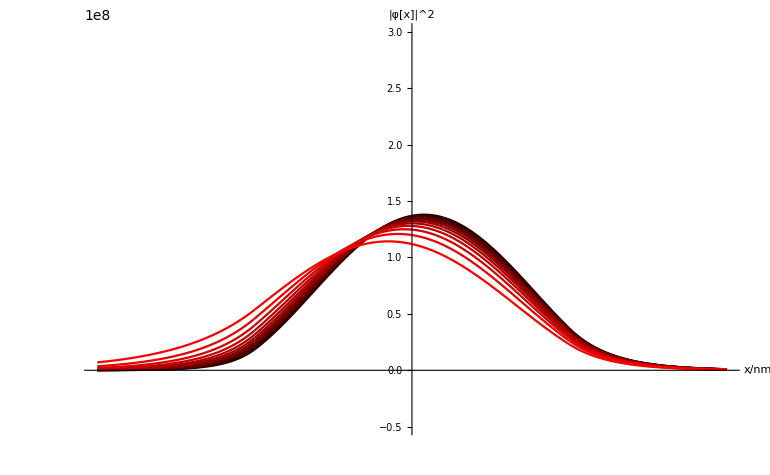

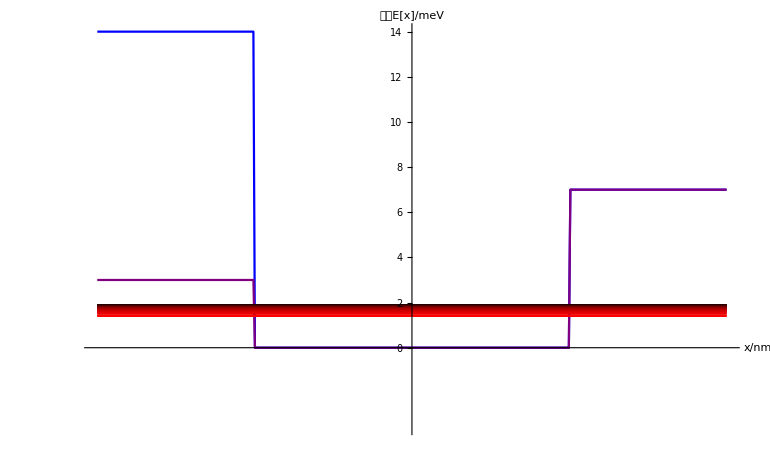

```mathematica
(*=======选择某一个定态 绘制波函数==============*)
Clear[En];
While[
En=Input["输入2个值，表示需要绘制的图或系列图，按 Ctrl+Enter 换行输入，
2个值均应大于0，小于束缚态数量，n=1 时为基态"];
Which[Element[En[[1,1]]+En[[2,1]], Integers]&&En[[1,1]]+En[[2,1]]>0&&En[[2,1]]/ En[[1,1]]>=1&&En[[2,1]]<=Length[Ex],Break[],True,CreateDialog[Column[{"输入两个数值不符合规范，第一个值应小于第二个值，且均为正整数",DefaultButton[]}]]]
]

Clear[pdi,pdpi,pdei,pd02,pd02i];
pdi=Table[pdie,0];(*存放波函数图像*)
pdpi=Table[pdpie,0];(*存放粒子出现概率图像*)
pdei=Table[pdeie,0];(*存放粒子能量图像*)
pd02i=Table[pd02ie,0];(*存放势函数变化图像*)

Clear[hison,his,hor,ver,verp,verv,perpt,trmatrix];
perpt=Table[perpti,0];
trmatrix={{1,0},{-0.5,1}};
trmatrix//MatrixForm;
Clear[α01,β01,γ01,δ01,η01,β011,δ011];

(*==========================      求解归一化系数      ==========================*)

For[i3=En[[1,1]],i3≤En[[2,1]],i3++,
Which[cha=="0",
V00t=Append[V00t,V00t[[1]]];
V01t=Append[V01t,V01t[[1]]];
V02t=Append[V02t,V02t[[1]]];
V03t=Append[V03t,V03t[[1]]];
at=Append[at,at[[1]]];
bt=Append[bt,bt[[1]]];
ct=Append[ct,ct[[1]]];
];


α01=Sqrt[2*me*Ex[[i3]]/(hb^2)];
β01=Sqrt[2*me*(V00t[[i3]]-Ex[[i3]])/hb^2];
γ01=Sqrt[2*me*(V01t[[i3]]-Ex[[i3]])/(hb^2)];
δ01=Sqrt[2*me*(V03t[[i3]]-Ex[[i3]])/hb^2];
 η01=Sqrt[2*me*(V02t[[i3]]-Ex[[i3]])/(hb^2)];

β011=Sqrt[2*me*(Ex[[i3]]-V00t[[i3]])/hb^2];
δ011=Sqrt[2*me*(Ex[[i3]]-V03t[[i3]])/hb^2];


Clear[Wj1,Wj2,Wj3,Wjr,Wsols];
Wj1={{E^(-γ01 bt[[i3]]),-Cos[α01 bt[[i3]]],Sin[α01 bt[[i3]]],0,0,0,0,0},{E^(-γ01 bt[[i3]]) γ01,-α01 Sin[α01 bt[[i3]]],-α01 Cos[α01 bt[[i3]]],0,0,0,0,0},{0,Cos[α01 at[[i3]]],-Sin[α01 at[[i3]]],-E^(-β01 at[[i3]]),-E^(β01 at[[i3]]),0,0,0},{0,α01 Sin[α01 at[[i3]]],α01 Cos[α01 at[[i3]]],-E^(-β01 at[[i3]]) β01,E^(β01 at[[i3]]) β01,0,0,0},{0,0,0,E^(β01 at[[i3]]),E^(-β01 at[[i3]]),-E^(δ01 at[[i3]]),-E^(-δ01 at[[i3]]),0},{0,0,0,E^(β01 at[[i3]]) β01,-E^(-β01 at[[i3]]) β01,-E^(δ01 at[[i3]]) δ01,E^(-δ01 at[[i3]]) δ01,0},{0,0,0,0,0,E^(δ01 ct[[i3]]),E^(-δ01 ct[[i3]]),-E^(-η01 ct[[i3]])},{0,0,0,0,0,E^(δ01 ct[[i3]]) δ01,-E^(-δ01 ct[[i3]]) δ01,E^(-η01 ct[[i3]]) η01}};

Wj2={{E^(-γ01 bt[[i3]]),-Cos[α01 bt[[i3]]],Sin[α01 bt[[i3]]],0,0,0,0,0},{E^(-γ01 bt[[i3]]) γ01,-α01 Sin[α01 bt[[i3]]],-α01 Cos[α01 bt[[i3]]],0,0,0,0,0},{0,Cos[α01 at[[i3]]],-Sin[α01 at[[i3]]],-E^(-β01 at[[i3]]),-E^(β01 at[[i3]]),0,0,0},{0,α01 Sin[α01 at[[i3]]],α01 Cos[α01 at[[i3]]],-E^(-β01 at[[i3]]) β01,E^(β01 at[[i3]]) β01,0,0,0},{0,0,0,E^(β01 at[[i3]]),E^(-β01 at[[i3]]),-Cos[δ011 at[[i3]]],-Sin[δ011 at[[i3]]],0},{0,0,0,E^(β01 at[[i3]]) β01,-E^(-β01 at[[i3]]) β01,δ011 Sin[δ011 at[[i3]]],-δ011 Cos[δ011 at[[i3]]],0},{0,0,0,0,0,Cos[δ011 ct[[i3]]],Sin[δ011 ct[[i3]]],-E^(-η01 ct[[i3]])},{0,0,0,0,0,-δ011 Sin[δ011 ct[[i3]]],δ011 Cos[δ011 ct[[i3]]],E^(-η01 ct[[i3]]) η01}};

Wj3={{E^(-γ01 bt[[i3]]),-Cos[α01 bt[[i3]]],Sin[α01 bt[[i3]]],0,0,0,0,0},{E^(-γ01 bt[[i3]]) γ01,-α01 Sin[α01 bt[[i3]]],-α01 Cos[α01 bt[[i3]]],0,0,0,0,0},{0,Cos[α01 at[[i3]]],-Sin[α01 at[[i3]]],-Cos[β011 at[[i3]]],Sin[β011 at[[i3]]],0,0,0},{0,α01 Sin[α01 at[[i3]]],α01 Cos[α01 at[[i3]]],-β011 Sin[β011 at[[i3]]],-β011 Cos[β011 at[[i3]]],0,0,0},{0,0,0,Cos[β011 at[[i3]]],Sin[β011 at[[i3]]],-Cos[δ011 at[[i3]]],-Sin[δ011 at[[i3]]],0},{0,0,0,-β011 Sin[β011 at[[i3]]],β011 Cos[β011 at[[i3]]],δ011 Sin[δ011 at[[i3]]],-δ011 Cos[δ011 at[[i3]]],0},{0,0,0,0,0,Cos[δ011 ct[[i3]]],Sin[δ011 ct[[i3]]],-E^(-η01 ct[[i3]])},{0,0,0,0,0,-δ011 Sin[δ011 ct[[i3]]],δ011 Cos[δ011 ct[[i3]]],E^(-η01 ct[[i3]]) η01}};
Clear[Wj];
Which[Ex[[i3]]<V03t[[i3]],Wj=Wj1,V03t[[i3]]<Ex[[i3]]<V00t[[i3]],Wj=Wj2,Ex[[i3]]>V00t[[i3]],Wj=Wj3];

MatrixForm[Wj];
Wjr=RowReduce[Wj,Tolerance->10^toler];
MatrixForm[Wjr];
Which[Wjr[[7,8]]==0,CreateDialog[Column[{"矩阵行约化计算精度过小，请提高",DefaultButton[]}]]];

Clear[Wsolst,Wsols];
Wsolst=Table[Wsolste,0];(*提取并存放8个待定系数*)
For[i=1,i≤8,i++,
If[i<8,Wsolst=Append[Wsolst,-Wjr[[i,8]]],
Wsolst=Append[Wsolst,1]]
];

(*归一化波函数*)
Clear[f01,f02,f03,f04,f05,Dx,Ax0];
f01=Integrate[(Wsolst[[1]]*Exp[γ01*x0])^2,{x0,-Infinity,-bt[[i3]]}];
f02=Integrate[(Wsolst[[2]]*Cos[α01*x0]+Wsolst[[3]]*Sin[α01*x0])^2,{x0,-bt[[i3]],-at[[i3]]}];
Which[
Ex[[i3]]<V03t[[i3]],
f03=Integrate[(Wsolst[[4]]*Exp[β01*x0]+Wsolst[[5]]*Exp[-β01*x0])^2,{x0,-at[[i3]],at[[i3]]}];
f04=Integrate[(Wsolst[[6]]*Exp[δ01*x0]+Wsolst[[7]]*Exp[-δ01*x0])^2,{x0,at[[i3]],ct[[i3]]}],

V03t[[i3]]<Ex[[i3]]<V00t[[i3]],
f03=Integrate[(Wsolst[[4]]*Exp[β01*x0]+Wsolst[[5]]*Exp[-β01*x0])^2,{x0,-at[[i3]],at[[i3]]}];
f04=Integrate[(Wsolst[[6]]*Cos[δ011*x0]+Wsolst[[7]]*Sin[δ011*x0])^2,{x0,at[[i3]],ct[[i3]]}],

Ex[[i3]]>V00t[[i3]],
f03=Integrate[(Wsolst[[4]]*Cos[β011*x0]+Wsolst[[5]]*Sin[β011*x0])^2,{x0,-at[[i3]],at[[i3]]}];
f04=Integrate[(Wsolst[[6]]*Cos[δ011*x0]+Wsolst[[7]]*Sin[δ011*x0])^2,{x0,at[[i3]],ct[[i3]]}]
];

f05=Integrate[(Wsolst[[8]]*Exp[-η01*x0])^2,{x0,ct[[i3]],Infinity}];

Dx=NSolve[(f01+f02+f03+f04+f05)*Ax^2==1,Ax];
Ax0=Dx[[1,1,2]];
Print["数值解："];
Wsolst;
Wsols=Wsolst*Ax0;


Clear[fd1,fd2,fd3,pd,
pfd1,pfd2,pfd3,pdp,
pde,
fd0,pd0,fd01,pd01,Li3];
(*======================== 绘制 -  透视图 ==========================*)
Which[(En[[2,1]]-En[[1,1]]+1)<=2,his=0,
En[[2,1]]-En[[1,1]]+1>2&&i3==En[[1,1]],
hison=Input["绘制的图像超过2幅，是否启用历史演化？
启用请输入“1”，不启用请输入“0”"]];
Which[hison==1,his=i3-En[[1,1]],hison==0,his=0];

hor=his*t*0;(*图像水平移动*)
ver=his*10^3;(*函数图像垂直移动*)
verp=his*10^7*5;(*概率图像垂直移动*)
verv=his*10^(-22)*3;(*势阱图像垂直移动*)

(*======================== 波函数 ==========================*)
fd1=Piecewise[{{Wsols[[1]]*Exp[γ01*(x0-hor)],-Infinity<x0≤-bt[[i3]]+hor},
{Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)],-bt[[i3]]-hor<x0≤-at[[i3]]+hor},
{Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)],-at[[i3]]+hor<x0≤at[[i3]]+hor},
{Wsols[[6]]*Exp[δ01*(x0-hor)]+Wsols[[7]]*Exp[-δ01*(x0-hor)],at[[i3]]+hor<x0≤ct[[i3]]+hor},
{Wsols[[8]]*Exp[-η01*(x0-hor)],ct[[i3]]+hor<x0<Infinity}}];
fd2=Piecewise[{{Wsols[[1]]*Exp[γ01*(x0-hor)],-Infinity<x0≤-bt[[i3]]+hor},
{Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)],-bt[[i3]]+hor<x0≤-at[[i3]]+hor},
{Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)],-at[[i3]]+hor<x0≤at[[i3]]+hor},
{Wsols[[6]]*Cos[δ011*(x0-hor)]+Wsols[[7]]*Sin[δ011*(x0-hor)],at[[i3]]+hor<x0≤ct[[i3]]+hor},
{Wsols[[8]]*Exp[-η01*(x0-hor)],ct[[i3]]+hor<x0<Infinity}}];
fd3=Piecewise[{{Wsols[[1]]*Exp[γ01*(x0-hor)],-Infinity<x0≤-bt[[i3]]+hor},
{Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)],-bt[[i3]]+hor<x0≤-at[[i3]]+hor},
{Wsols[[4]]*Cos[β011*(x0-hor)]+Wsols[[5]]*Sin[β011*(x0-hor)],-at[[i3]]+hor<x0≤at[[i3]]+hor},
{Wsols[[6]]*Cos[δ011*(x0-hor)]+Wsols[[7]]*Sin[δ011*(x0-hor)],at[[i3]]+hor<x0≤ct[[i3]]+hor},
{Wsols[[8]]*Exp[-η01*(x0-hor)],ct[[i3]]+hor<x0<Infinity}}];

Which[
Ex[[i3]]<V03t[[i3]],pd=Plot[fd1+ver,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["φ[x]",Bold,Black,foze]},PlotStyle->Hue[1,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}],
V03t[[i3]]<Ex[[i3]]<V00t[[i3]],
pd=Plot[fd2+ver,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["φ[x]",Bold,Black,foze]},PlotStyle->Hue[1,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}],
Ex[[i3]]>V00t[[i3]],
pd=Plot[fd3+ver,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotRange->All,PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["φ[x]",Bold,Black,foze]},PlotStyle->Hue[1,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}]
];

pdi=Append[pdi,pd];

(*(*===========================检查函数连续性===========================*)
Clear[ff01,ff02,ff03,ff04,ff05];
ff01=Function[x0,Wsols[[1]]*Exp[γ01*(x0-hor)]];
ff02=Function[x0,Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)]];

Which[
Ex[[i3]]<V03,
ff03=Function[x0,Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)]];
ff04=Function[x0,Wsols[[6]]*Exp[δ01*(x0-hor)]+Wsols[[7]]*Exp[-δ01*(x0-hor)]],
V03<Ex[[i3]]<V00,
ff03=Function[x0,Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)]];
ff04=Function[x0,Wsols[[6]]*Cos[δ01*(x0-hor)]+Wsols[[7]]*Sin[δ01*(x0-hor)]],
Ex[[i3]]>V00,
ff03=Function[x0,Wsols[[4]]*Cos[β01*(x0-hor)]+Wsols[[5]]*Sin[β01*(x0-hor)]];
ff04=Function[x0,Wsols[[6]]*Cos[δ01*(x0-hor)]+Wsols[[7]]*Sin[δ01*(x0-hor)]];
];

ff05=Function[x0,Wsols[[8]]*Exp[-η01*(x0-hor)]];

Print["-b1 ",ff01[-b1],"\n","差值：",ff01[-b1]-ff02[-b1],"\n"];
Print["-a1 ",ff02[-a1],"\n","差值：",ff02[-a1]-ff03[-a1],"\n"];
Print["a1  ",ff03[a1],"\n","差值：",ff03[a1]-ff04[a1],"\n"];
Print["c1  ",ff04[c1],"\n","差值：",ff04[c1]-ff05[c1]];*)


(*======================== 概率分布 ==========================*)
pfd1=Piecewise[{{(Wsols[[1]]*Exp[γ01*(x0-hor)])^2,-Infinity<x0≤-bt[[i3]]+hor},
{(Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)])^2,-bt[[i3]]+hor<x0≤-at[[i3]]+hor},{(Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)])^2,-at[[i3]]+hor<x0≤at[[i3]]+hor},{(Wsols[[6]]*Exp[δ01*(x0-hor)]+Wsols[[7]]*Exp[-δ01*(x0-hor)])^2,at[[i3]]+hor<x0≤ct[[i3]]+hor},
{(Wsols[[8]]*Exp[-η01*(x0-hor)])^2,ct[[i3]]+hor<x0<Infinity}}];
pfd2=Piecewise[{{(Wsols[[1]]*Exp[γ01*(x0-hor)])^2,-Infinity<x0≤-bt[[i3]]+hor},
{(Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)])^2,-bt[[i3]]+hor<x0≤-at[[i3]]+hor},
{(Wsols[[4]]*Exp[β01*(x0-hor)]+Wsols[[5]]*Exp[-β01*(x0-hor)])^2,-at[[i3]]+hor<x0≤at[[i3]]+hor},
{(Wsols[[6]]*Cos[δ011*(x0-hor)]+Wsols[[7]]*Sin[δ011*(x0-hor)])^2,at[[i3]]+hor<x0≤ct[[i3]]+hor},
{(Wsols[[8]]*Exp[-η01*(x0-hor)])^2,ct[[i3]]<x0<Infinity}}];
pfd3=Piecewise[{{(Wsols[[1]]*Exp[γ01*(x0-hor)])^2,-Infinity<x0≤-bt[[i3]]+hor},
{(Wsols[[2]]*Cos[α01*(x0-hor)]+Wsols[[3]]*Sin[α01*(x0-hor)])^2,-bt[[i3]]+hor<x0≤-at[[i3]]+hor},
{(Wsols[[4]]*Cos[β011*(x0-hor)]+Wsols[[5]]*Sin[β011*(x0-hor)])^2,-at[[i3]]+hor<x0≤at[[i3]]+hor},
{(Wsols[[6]]*Cos[δ011*(x0-hor)]+Wsols[[7]]*Sin[δ011*(x0-hor)])^2,at[[i3]]+hor<x0≤ct[[i3]]+hor},
{(Wsols[[8]]*Exp[-η01*(x0-hor)])^2,ct[[i3]]+hor<x0<Infinity}}];

Which[
Ex[[i3]]<V03t[[i3]],
pdp=Plot[pfd1+verp,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["|φ[x]|^2",Bold,Black,foze]},PlotStyle->Hue[0,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}],
V03t[[i3]]<Ex[[i3]]<V00t[[i3]],
pdp=Plot[pfd2+verp,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["|φ[x]|^2",Bold,Black,foze]},PlotStyle->Hue[0,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}],
Ex[[i3]]>V00t[[i3]],
pdp=Plot[pfd3+verp,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotPoints->500,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["|φ[x]|^2",Bold,Black,foze]},PlotStyle->Hue[0,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],Automatic}]
];
pdpi=Append[pdpi,pdp];

Which[i3==1,Print["【基态】能量","\n",Ex[[i3]]/J," meV"," 或 ",Ex[[i3]]," J","\n"],
i3>1,Print["【第",i3-1,"激发态】能量 ","\n",Ex[[i3]]/J," meV"," 或 ",Ex[[i3]]," J","\n"]];
pde=Plot[Ex[[i3]],{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotStyle->Hue[0,1,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],{#*J,#}&/@Range[0,Max[{hv1,hv5}]*2,2]}];
pdei=Append[pdei,pde];

(*===========================绘制 - 函数演变————透视变换================================*)

fd02=Piecewise[{{V01t[[i3]],-Infinity<x0<=-bt[[i3]]+hor},
{0,-bt[[i3]]+hor<x0≤-at[[i3]]+hor},
{V00t[[i3]],-at[[i3]]+hor<x0<=at[[i3]]+hor},
{V03t[[i3]],at[[i3]]+hor<x0<=ct[[i3]]+hor},
{V02t[[i3]],ct[[i3]]+hor<x0<Infinity}}];
pd02=Plot[fd02+verv,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotRange->{-0.5*Vp,1.5*Vp},PlotStyle->Hue[0.7,0.7,(i3-(En[[1,1]]-1))/(En[[2,1]]-En[[1,1]]+1)],Exclusions->None,PlotPoints->400,Axes->False];
pd02i=Append[pd02i,pd02];

Which[hison==1,
perpt=Append[perpt,ImagePerspectiveTransformation[GraphicsColumn[{Show[pdpi[[i3-(En[[1,1]]-1)]],PlotRange->{-0.5*10^prova,6*10^prova},Axes->False],Show[pd02i[[i3-(En[[1,1]]-1)]],PlotRange->{-0.5*Vp,1.5*Vp},Axes->False]}],trmatrix,300,PlotRange->All,DataRange->Full]];
];
];

Clear[Li3];
Li3=En[[2,1]];

Print["共",En[[2,1]]-En[[1,1]]+1,"个态","\n"];

(*===========================绘制 - 势阱函数================================*)
(*Print["边界点：","a1：",N[a1]," ，","b1：",N[b1]," ，","c1：",N[c1],"\n"]*)
Print["【起始势阱形状】",
"\n","左边阱宽：",N[(bt[[1]]-at[[1]])/t],"(纳米)，","阱距"：,N[2*at[[1]]/t],"(纳米)，","右边阱宽：",N[(ct[[1]]-at[[1]])/t],"(纳米)，","\n",
"左势垒",V01t[[1]]/J,"(meV)，",V01t[[1]],"(J)，","\n",
"左势阱",0,"(meV)，",0"(J)，","\n",
"中间势垒",V00t[[1]]/J,"(meV)，",V00t[[1]],"(J)，","\n",
"右势阱",V03t[[1]]/J,"(meV)，",V03t[[1]],"(J)，","\n",
"右势垒",V02t[[1]]/J,"(meV)，",V02t[[1]],"(J)","\n"];
Print["【结束势阱形状】",
"\n","左边阱宽：",N[(bt[[Li3]]-at[[Li3]])/t],"(纳米)，","阱距"：,N[2*at[[Li3]]/t],"(纳米)，","右边阱宽：",N[(ct[[Li3]]-at[[Li3]])/t],"(纳米)，","\n",
"左势垒",V01t[[Li3]]/J,"(meV)，",V01t[[Li3]],"(J)，","\n",
"左势阱",0,"(meV)，",0"(J)，","\n",
"中间势垒",V00t[[Li3]]/J,"(meV)，",V00t[[Li3]],"(J)，","\n",
"右势阱",V03t[[Li3]]/J,"(meV)，",V03t[[Li3]],"(J)，","\n",
"右势垒",V02t[[Li3]]/J,"(meV)，",V02t[[Li3]],"(J)"];


fd0=Piecewise[{{V01t[[1]],-Infinity<x0<=-bt[[1]]+hor},
{0,-bt[[1]]+hor<x0≤-at[[1]]+hor},
{V00t[[1]],-at[[1]]+hor<x0<=at[[1]]+hor},
{V03t[[1]],at[[1]]+hor<x0<=ct[[1]]+hor},
{V02t[[1]],ct[[1]]+hor<x0<Infinity}}];
fd01=Piecewise[{{V01t[[Li3]],-Infinity<x0<=-bt[[Li3]]+hor},
{0,-bt[[Li3]]+hor<x0≤-at[[Li3]]+hor},
{V00t[[Li3]],-at[[Li3]]+hor<x0<=at[[Li3]]+hor},
{V03t[[Li3]],at[[Li3]]+hor<x0<=ct[[Li3]]+hor},
{V02t[[Li3]],ct[[Li3]]+hor<x0<Infinity}}];

Clear[Vp];
Vp=Max[V01,V00,V03,V02];
pd0=Plot[fd0,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotRange->{-0.5*Vp,2*Vp},PlotStyle->Blue,Exclusions->None,PlotPoints->400,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["能量E[x]/meV",Bold,Black,foze]},Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],{#*J,#}&/@Range[0,Max[{hv1,hv5}]*2,2]}
(*,PlotLabel->"起始势函数"*)];
pd01=Plot[fd01,{x0,(-bt[[1]])*2,(ct[[1]]+hor)*2},PlotRange->{-0.5*Vp,2*Vp},PlotStyle->Purple,Exclusions->None,PlotPoints->400,AxesLabel->{Style["x/nm",Bold,Black,foze],Style["能量E[x]/meV",Bold,Black,foze]},PlotLabel->"结束势函数",Ticks->{{#*t,#}&/@Range[(-lwei-mwei/2)*14,(rwei+mwei/2)*14,1],{#*J,#}&/@Range[0,Max[{hv1,hv5}]*2,2]}];


GraphicsGrid[{{Show[pdi,PlotRange->{-1.6*10^wava,1.6*10^wava}],Show[pdpi,PlotRange->{-0.5*10^prova,6*10^prova}]},{Show[pd0,pd01,pdei],Show[pd0,pd01,pdei]}},Frame->All]

Which[hison==1,Print["粒子出现概率演化图像如下"];Print[Show[perpt]],
hison==0,Print["历史演化图像：没有启用。呈现初状态与末状态的对比"];
Print[GraphicsColumn[{
Show[pdpi[[1]],pdpi[[Li3]],PlotRange->{-0.5*10^prova,3*10^prova}],
Show[Show[pd0,pdei[[1]]],Show[pd01,pdei[[Li3]]]]
}]]];

Show[pdpi,PlotRange->{-0.5*10^prova,3*10^prova}]
Show[Show[pd0,pdei],Show[pd01,pdei]]


(*Show[pdi]*)
(*Show[pd0,pdei]*)
(*Show[pdpi,Show[ContourPlot[x==-bt[[1]],{x,-bt[[1]]*2,ct[[1]]*2},{y,-0.5*10^prova,3*10^prova},Axes->True,Frame->False,ContourStyle->{Orange,Dashed}],
ContourPlot[x==-at[[1]],{x,-bt[[1]]*2,ct[[1]]*2},{y,-0.5*10^prova,3*10^prova},Axes->True,Frame->False,ContourStyle->{Orange,Dashed}],
ContourPlot[x==at[[1]],{x,-bt[[1]]*2,ct[[1]]*2},{y,-0.5*10^prova,3*10^prova},Axes->True,Frame->False,ContourStyle->{Orange,Dashed}],
ContourPlot[x==ct[[1]],{x,-bt[[1]]*2,ct[[1]]*2},{y,-0.5*10^prova,3*10^prova},Axes->True,Frame->False,ContourStyle->{Orange,Dashed}]]]*)
```